```mathematica
ClearAll["Global`","Subscript"]
```

```mathematica
eq = j'(j'-1) == j(j+1)
```

(-1+j') j'==j (1+j)

```mathematica
Solve[eq, j']//Flatten
```

{j'→-j,j'→1+j}

*********************************

```mathematica
$Assumptions = b[Subscript[ψ, -1/2]] ≠ 0 && b[Subscript[ψ, 1/2]] ≠ 0
```

b[ψ_(-1/2)]≠0&&b[ψ_(1/2)]≠0

```mathematica
eq1 = (Subscript[J, 1] +I Subscript[J, 2]) Subscript[ψ, -1/2]== ℏ Subscript[ψ, 1/2]
```

(J_1+ⅈ J_2) ψ_(-1/2)==ℏ ψ_(1/2)

```mathematica
eq2 = (Subscript[J, 1] -I Subscript[J, 2]) Subscript[ψ, 1/2]== ℏ Subscript[ψ, -1/2]
```

(J_1-ⅈ J_2) ψ_(1/2)==ℏ ψ_(-1/2)

```mathematica
eq3 = (Subscript[J, 1] +I Subscript[J, 2]) Subscript[ψ, 1/2]== 0
```

(J_1+ⅈ J_2) ψ_(1/2)==0

```mathematica
eq4 = (Subscript[J, 1] - I Subscript[J, 2]) Subscript[ψ, -1/2]== 0
```

(J_1-ⅈ J_2) ψ_(-1/2)==0

```mathematica
b[ Subscript[ψ, m_]]  Subscript[ψ, m1_] ^:= 1 /;m==m1
b[ Subscript[ψ, m_]] Subscript[J, j_]  Subscript[ψ, m1_] ^:= sp[Subscript[ψ, m], Subscript[J, j] Subscript[ψ, m1]] /;m!=m1
```

```mathematica
b[ Subscript[ψ, m_]]  Subscript[ψ, m1_] ^:= 0 /;m!=m1
```

```mathematica
AddSides[eq1,eq4]//Simplify
```

2 J_1 ψ_(-1/2)==ℏ ψ_(1/2)

```mathematica
MultiplySides[%,b[ Subscript[ψ, 1/2]] ]
```

2 sp[ψ_(1/2),J_1 ψ_(-1/2)]==ℏ

```mathematica
AddSides[eq2,eq3]//Simplify
```

ℏ ψ_(-1/2)==2 J_1 ψ_(1/2)

```mathematica
MultiplySides[%,b[ Subscript[ψ, -1/2]] ]
```

ℏ==2 sp[ψ_(-1/2),J_1 ψ_(1/2)]

```mathematica
SubtractSides[eq1,eq4]//Simplify
```

2 ⅈ J_2 ψ_(-1/2)==ℏ ψ_(1/2)

```mathematica
MultiplySides[%,b[ Subscript[ψ, 1/2]] ]
```

2 ⅈ sp[ψ_(1/2),J_2 ψ_(-1/2)]==ℏ

```mathematica
SubtractSides[eq2,eq3]//Simplify
```

-2 ⅈ J_2 ψ_(1/2)==ℏ ψ_(-1/2)

```mathematica
MultiplySides[%,b[ Subscript[ψ, -1/2]] ]
```

-2 ⅈ sp[ψ_(-1/2),J_2 ψ_(1/2)]==ℏ

*************************************************

```mathematica
Clear[i,j,m]
```

```mathematica
Subscript[D, ij] = Table[Subscript[D, i,j],{i,1,3},{j,1,3}]
```

{{D_(1,1),D_(1,2),D_(1,3)},{D_(2,1),D_(2,2),D_(2,3)},{D_(3,1),D_(3,2),D_(3,3)}}

```mathematica
%//MatrixForm
```

(D_(1,1) | D_(1,2) | D_(1,3)
D_(2,1) | D_(2,2) | D_(2,3)
D_(3,1) | D_(3,2) | D_(3,3))

```mathematica
X = {Subscript[x, 1],Subscript[x, 2],Subscript[x, 3]}
```

{x_1,x_2,x_3}

```mathematica
Subscript[B, l] = Subscript[D, ij].X
```

{x_1 D_(1,1)+x_2 D_(1,2)+x_3 D_(1,3),x_1 D_(2,1)+x_2 D_(2,2)+x_3 D_(2,3),x_1 D_(3,1)+x_2 D_(3,2)+x_3 D_(3,3)}

```mathematica
Div[Subscript[B, l],{Subscript[x, 1],Subscript[x, 2],Subscript[x, 3]}]/. Subscript[D, 1,1]+Subscript[D, 2,2]+Subscript[D, 3,3] -> 0
```

0

```mathematica
Curl[Subscript[B, l],{Subscript[x, 1],Subscript[x, 2],Subscript[x, 3]}]/.Subscript[D, i_,j_]/;i>j -> Subscript[D, j,i]
```

{0,0,0}

```mathematica
eq =m D[Subscript[x, i][t], {t,2}] == (μ σ)/j Subscript[D, 3,i]
```

m x_i''[t]==(μ σ D_(3,i))/j

```mathematica
DSolve[{eq, Subscript[x, i][0] ==0}, Subscript[x, i][t], t]//Flatten
```

{x_i[t]→(2 j m t C[2]+t^2 μ σ D_(3,i))/(2 j m)}

```mathematica
sol = %/.{ m->1, Subscript[D, i_,j_]->1, C[2]->1, j->1/2, μ ->1}
```

{x_i[t]→t+t^2 σ}

```mathematica
Subscript[x, 1] = Subscript[x, i][t]/.sol/.{i->1}
```

t+t^2 σ

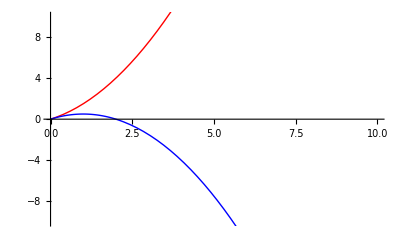

```mathematica
Show[Plot[Subscript[x, 1]/.σ->1/2, {t, 0, 10}, PlotStyle->{Red,Thick}],
Plot[Subscript[x, 1]/.σ->-1/2, {t, 0, 10},PlotStyle->{Blue,Thick}], PlotRange->{-10, 10}]
```